{h→0.002,r1→0.2,r2→0.4,R1→∞,L→0.4,Emod→200000000000,μ→0.3,ρ→1000,g→9.81}

Piecewise[{{0, 0<y<r}, {g y ρ, -r<y<0}, {0, True}}]

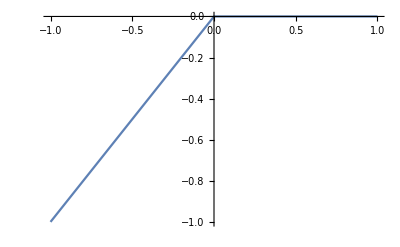

```mathematica
(*График давленьица от высоты*)
Data={h->0.002,r1->0.200,r2->0.400,R1->Infinity,L->0.400,Emod->2*10^11,μ->0.3,ρ->1000,g->9.81}
plotData={r1->1,r2->2,g->1,ρ->1,r->1,L->1};
(*Нагрузка*)
qny[y_]=Piecewise[{{0,0<y<r},{ρ*g*y,-r<y<0}}]
Plot[qny[y]/.plotData,{y,-r,r}/.plotData]
```

Piecewise[{{-g r ρ Cos[ϕ], 0<Cos[ϕ]<1}, {0, True}}]

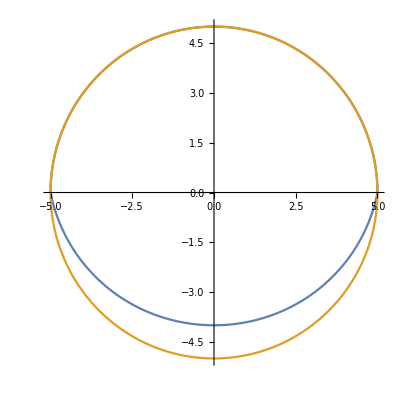

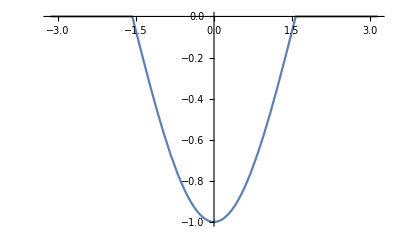

```mathematica
(*Нагрузка через угловую координату. Начало координат в нижней точке для симметрии*)
qn[ϕ_]=Simplify[qny[y]/.y->r*Cos[ϕ-Pi],Assumptions->{r>0,y>0,Element[ϕ,Reals]}]
PolarPlot[{5+qn[ϕ+Pi/2]/.plotData,5},{ϕ,0,2*Pi}]
Plot[qn[ϕ]/.plotData,{ϕ,-Pi,Pi}]
```

-(g r ρ)/π-1/2 g r ρ Cos[ϕ]-(2 g r ρ Cos[2 ϕ])/(3 π)+(2 g r ρ Cos[4 ϕ])/(15 π)-(2 g r ρ Cos[6 ϕ])/(35 π)+(2 g r ρ Cos[8 ϕ])/(63 π)

{-(g r ρ)/π,-1/2 g r ρ,-(2 g r ρ)/(3 π),0,(2 g r ρ)/(15 π),0,-(2 g r ρ)/(35 π),0}

{1,Cos[ϕ],Cos[2 ϕ],Cos[3 ϕ],Cos[4 ϕ],Cos[5 ϕ],Cos[6 ϕ],Cos[7 ϕ]}

{0,Sin[ϕ],Sin[2 ϕ],Sin[3 ϕ],Sin[4 ϕ],Sin[5 ϕ],Sin[6 ϕ],Sin[7 ϕ]}

-(g r ρ)/π-1/2 g r ρ Cos[ϕ]-(2 g r ρ Cos[2 ϕ])/(3 π)+(2 g r ρ Cos[4 ϕ])/(15 π)-(2 g r ρ Cos[6 ϕ])/(35 π)

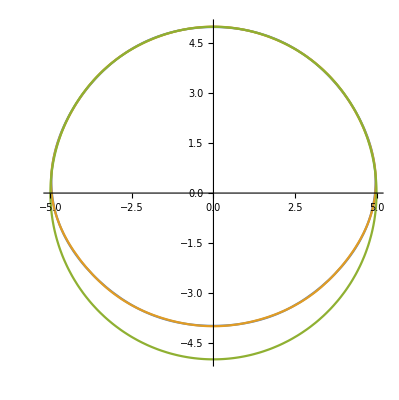

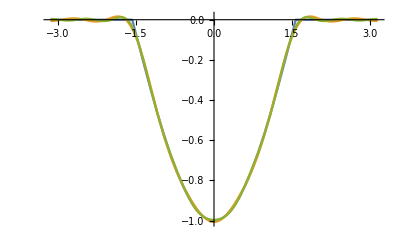

```mathematica
(*Разложим нагрузку в ряд Фурье*)
terms=8;
qnF2[ϕ_]=FourierCosSeries[qn[ϕ],ϕ,terms]
(*То же самое, но ручками*)
qnCoeffs=FourierCosCoefficient[qn[ϕ],ϕ,#]&/@Range[0,terms-1];
qnCoeffs[[1]]=1/2*qnCoeffs[[1]];
qnCoeffs
cosines[ϕ_]=Cos[#*ϕ]&/@Range[0,terms-1]
sines[ϕ_]=Sin[#*ϕ]&/@Range[0,terms-1] (*Пригодятся потом для складывания найденных величин*)
qnF[ϕ_]=qnCoeffs.cosines[ϕ]
PolarPlot[{5+qnF[ϕ+Pi/2]/.plotData,5+qnF2[ϕ+Pi/2]/.plotData,5},{ϕ,0,2*Pi}]
Plot[{qn[ϕ]/.plotData,qnF[ϕ]/.plotData,qnF2[ϕ]/.plotData},{ϕ,-Pi,Pi}]
```

```mathematica
(*Выражаем r через r1 и r2*)
θ=Pi/2-ArcTan[(r2-r1)/L]/.Data
rData=Simplify[{r->r1+S*Sin[ArcTan[(r2-r1)/L]/.Data]},Assumptions->{r>0,r1>0,r2>0}]
Smax=L/Sin[θ]/.Data
Simplify[r/.rData/.S->Smax,Assumptions->{r>0,r1>0,r2>0}]
θ//N
```

1.10715

{r→r1+0.447214 S}

0.447214

0.2+r1

1.10715

```mathematica
(*Чекаем реальную нагрузку*)
FourierCosCoefficient[qn[ϕ],ϕ,#]&/@Range[0,terms-1];
qnCoeffs2=FourierCosCoefficient[qn[ϕ],ϕ,#]&/@Range[0,terms-1]/.rData/.Data/.S->Smax;
qnCoeffs2[[1]]=1/2*qnCoeffs2[[1]];
qnCoeffs2
qmax=Total[qnCoeffs2]
```

{-1249.05,-1962.,-832.699,0,166.54,0,-71.3742,0}

-3948.58

```mathematica
(*Нарисуем конус и проверим*)
Xcone=r*Sin[ϕ]/.rData/.Data
Ycone=-r*Cos[ϕ]/.rData/.Data
Zcone=S*Cos[Pi/2-θ]/.rData/.Data
conePlot=ParametricPlot3D[{Xcone,Ycone,Zcone},{ϕ,-Pi,Pi},{S,0,Smax/.Data},AxesLabel->{"x","y","z"}];
waterPlot=Graphics3D[{Blue,Arrow[Tube[{{0,0,Smax/2/.Data},{0,-100,Smax/2/.Data}}]] }];
Show[{conePlot,waterPlot}]
(*Show[{waterPlot,conePlot}]*)
```

(0.2+0.447214 S) Sin[ϕ]

-(0.2+0.447214 S) Cos[ϕ]

0.894427 S

-Graphics3D-

-0.31831 g r1 ρ-0.142353 g S ρ-0.5 g r1 ρ Cos[ϕ]-0.223607 g S ρ Cos[ϕ]-0.212207 g r1 ρ Cos[2 ϕ]-0.0949017 g S ρ Cos[2 ϕ]+0.0424413 g r1 ρ Cos[4 ϕ]+0.0189803 g S ρ Cos[4 ϕ]-0.0181891 g r1 ρ Cos[6 ϕ]-0.00813443 g S ρ Cos[6 ϕ]

-624.524-1396.48 S-981. Cos[ϕ]-2193.58 S Cos[ϕ]-416.349 Cos[2 ϕ]-930.985 S Cos[2 ϕ]+83.2699 Cos[4 ϕ]+186.197 S Cos[4 ϕ]-35.6871 Cos[6 ϕ]-79.7987 S Cos[6 ϕ]

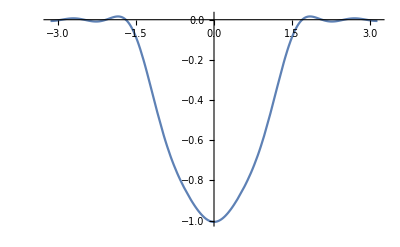

```mathematica
(*Тогда нагрузка через S и ϕ*)
q[S_,ϕ_]=Simplify[qnF[ϕ]/.rData,Assumptions->{r1>0,r2>0,S>0,L>0}]//Expand
q[S,ϕ]/.Data
Plot[qnF[ϕ]/.plotData/.S->0,{ϕ,-Pi,Pi}]
```

```mathematica
(*Вектор состояния и его производная*)
yk[S_]={uk[S],wk[S],vk[S],υ1k[S],T1k[S]*r,Q1k[S]*r,S1k[S]*r,M1k[S]*r}/.rData/.Data
ykd[S_]=D[yk[S],S]
ykd[S]
```

{uk[S],wk[S],vk[S],υ1k[S],(0.2+0.447214 S) T1k[S],(0.2+0.447214 S) Q1k[S],(0.2+0.447214 S) S1k[S],(0.2+0.447214 S) M1k[S]}

{uk'[S],wk'[S],vk'[S],υ1k'[S],0.447214 T1k[S]+(0.2+0.447214 S) T1k'[S],0.447214 Q1k[S]+(0.2+0.447214 S) Q1k'[S],0.447214 S1k[S]+(0.2+0.447214 S) S1k'[S],0.447214 M1k[S]+(0.2+0.447214 S) M1k'[S]}

{uk'[S],wk'[S],vk'[S],υ1k'[S],0.447214 T1k[S]+(0.2+0.447214 S) T1k'[S],0.447214 Q1k[S]+(0.2+0.447214 S) Q1k'[S],0.447214 S1k[S]+(0.2+0.447214 S) S1k'[S],0.447214 M1k[S]+(0.2+0.447214 S) M1k'[S]}

```mathematica
(*Матрица уравнения*)
Fk[S_]={
(*1-я*){-μ*Cos[θ]/r, -μ*k/r, -1/R1-μ*Sin[θ]/r, 0, (1-μ^2)/(Emod*h*r), 0, 0, 0},
(*2-я*){k/r, Cos[θ]/r, 0, 0, 0, 2*(1+μ)/(Emod*h*r), 0, 0},
(*3-я*){1/R1, 0, 0, -1, 0, 0, 0, 0},
(*4-я*){0, -μ*k/r^2*Sin[θ],μ*k^2/r^2, -μ*Cos[θ]/r , 0, 0, 0, 12*(1-μ^2)/(Emod*h^3*r)},
(*5-я*){Emod*h/r*(Cos[θ]^2+k^2*h^2*Sin[θ]^2/(6*(1+μ)*r^2))(*|*), k*Emod*h/r*Cos[θ](*|*), Emod*h/r*Sin[θ]*Cos[θ]*(1-k^2*h^2/(6*(1+μ)*r^2))(*|*), -k^2*Emod*h^3/(6*(1+μ)*r^2)*Sin[θ](*|*), μ/r*Cos[θ], -k/r, -1/R1, 0},
(*6-я*){Emod*h/r*k*Cos[θ](*|*), k^2*Emod*h/r(*|*), Emod*h/r*k*Sin[θ]*(1+k^2*h^2/(12*r^2))(*|*), Emod*h^3/(12*r^2)*k*Sin[θ]*Cos[θ], μ*k/r, -Cos[θ]/r, 0, μ*k/r^2*Sin[θ]},
(*7-я*) {k*Emod*h/r*Cos[θ]*Sin[θ]*(1-k^2*h^2/(6*(1+μ)*r^2))(*|*),Emod*h/r*k*Sin[θ]*(1+k^2*h^2/(12*r^2))(*|*),Emod*h/r*(Sin[θ]^2+k^4*h^2/(12*r^2)+k^2*h^2*Cos[θ]^2/(6*(1+μ)*r^2))(*|*),(3+μ)/(1+μ)*Emod*h^3/(12*r^2)*k^2*Cos[θ](*|*), 1/R1+μ*Sin[θ]/r, 0,0, μ*k^2/r^2},
(*8-я*){-k^2*Emod*h^3/(6*(1+μ)*r^2)*Sin[θ](*|*),Emod*h^3/(12*r^2)*k*Sin[θ]*Cos[θ](*|*),(3+μ)/(1+μ)*Emod*h^3/(12*r^2)*k^2*Cos[θ](*|*), Emod*h^3/(12*r)*(Cos[θ]^2+2*k^2/(1+μ))(*|*), 0, 0, 1, μ*Cos[θ]/r}
}/.rData/.Data//N;
Fk[S]/.k->1/.Data//MatrixForm
R1/.Data
Fk[S]/.k->1/.S->(Smax/2)/.Data//N//MatrixForm
```

(-0.134164/(0.2+0.447214 S) | -0.3/(0.2+0.447214 S) | -0.268328/(0.2+0.447214 S) | 0. | (2.275×10^-9)/(0.2+0.447214 S) | 0. | 0. | 0.
1/(0.2+0.447214 S) | 0.447214/(0.2+0.447214 S) | 0. | 0. | 0. | (6.5×10^-9)/(0.2+0.447214 S) | 0. | 0.
0. | 0. | 0. | -1. | 0. | 0. | 0. | 0.
0. | -0.268328/(0.2+0.447214 S)^2 | 0.3/(0.2+0.447214 S)^2 | -0.134164/(0.2+0.447214 S) | 0. | 0. | 0. | 0.006825/(0.2+0.447214 S)
(4.×10^8 (0.2+(4.10256×10^-7)/(0.2+0.447214 S)^2))/(0.2+0.447214 S) | (1.78885×10^8)/(0.2+0.447214 S) | (1.6×10^8 (1.-(5.12821×10^-7)/(0.2+0.447214 S)^2))/(0.2+0.447214 S) | -183.472/(0.2+0.447214 S)^2 | 0.134164/(0.2+0.447214 S) | -1./(0.2+0.447214 S) | 0. | 0.
(1.78885×10^8)/(0.2+0.447214 S) | (4.×10^8)/(0.2+0.447214 S) | (3.57771×10^8 (1.+(3.33333×10^-7)/(0.2+0.447214 S)^2))/(0.2+0.447214 S) | 53.3333/(0.2+0.447214 S)^2 | 0.3/(0.2+0.447214 S) | -0.447214/(0.2+0.447214 S) | 0. | 0.268328/(0.2+0.447214 S)^2
(1.6×10^8 (1.-(5.12821×10^-7)/(0.2+0.447214 S)^2))/(0.2+0.447214 S) | (3.57771×10^8 (1.+(3.33333×10^-7)/(0.2+0.447214 S)^2))/(0.2+0.447214 S) | (4.×10^8 (0.8+(4.35897×10^-7)/(0.2+0.447214 S)^2))/(0.2+0.447214 S) | 151.365/(0.2+0.447214 S)^2 | 0.268328/(0.2+0.447214 S) | 0. | 0. | 0.3/(0.2+0.447214 S)^2
-183.472/(0.2+0.447214 S)^2 | 53.3333/(0.2+0.447214 S)^2 | 151.365/(0.2+0.447214 S)^2 | 231.795/(0.2+0.447214 S) | 0. | 0. | 1. | 0.134164/(0.2+0.447214 S))

∞

(-0.447214 | -1. | -0.894427 | 0. | 7.58333×10^-9 | 0. | 0. | 0.
3.33333 | 1.49071 | 0. | 0. | 0. | 2.16667×10^-8 | 0. | 0.
0. | 0. | 0. | -1. | 0. | 0. | 0. | 0.
0. | -2.98142 | 3.33333 | -0.447214 | 0. | 0. | 0. | 0.02275
2.66673×10^8 | 5.96285×10^8 | 5.3333×10^8 | -2038.58 | 0.447214 | -3.33333 | 0. | 0.
5.96285×10^8 | 1.33333×10^9 | 1.19257×10^9 | 592.593 | 1. | -1.49071 | 0. | 2.98142
5.3333×10^8 | 1.19257×10^9 | 1.06667×10^9 | 1681.83 | 0.894427 | 0. | 0. | 3.33333
-2038.58 | 592.593 | 1681.83 | 772.65 | 0. | 0. | 1. | 0.447214)

```mathematica
(*Вектор нагрузок*)
g3k[S_]:={0,0,0,0,0,0,-r,0}*qnCoeffs[[k+1]]/.rData/.Data (*Тут к+1 из расчета, что гармоники нумеруются с нулевой*)
g3k[S]/.k->7
```

{0,0,0,0,0,0,0,0}

```mathematica
equationsk=Simplify[Thread[ykd[S]==Fk[S].yk[S]+g3k[S]],Assumptions->{k>0,S>0}]
```

{(447.214+1. S) T1k[S]==131868. uk[S]+263736. vk[S]+294866. k wk[S]+1.96577×10^8 uk'[S]+439560. S uk'[S],wk'[S]==((0.00290689+6.5×10^-6 S) Q1k[S]+2.23607 k uk[S]+1. wk[S])/(447.214+1. S),vk'[S]==0.-1. υ1k[S],υ1k'[S]==((1.365+0.00610447 S+6.825×10^-6 S^2) M1k[S]+1.5 k^2 vk[S]-1.34164 k wk[S]-134.164 υ1k[S]-0.3 S υ1k[S])/(447.214+1. S)^2,T1k[S]/(√5)+(200+S/(√5)) T1k'[S]==1/(447.214+1. S)^3(k (-8.94427×10^7-600000. S-1341.64 S^2-1. S^3) Q1k[S]+(1.2×10^7+80498.4 S+180. S^2+0.134164 S^3) T1k[S]+3.57771×10^10 uk[S]+1.83472×10^6 k^2 uk[S]+1.6×10^8 S uk[S]+178885. S^2 uk[S]+7.15542×10^10 vk[S]-917361. k^2 vk[S]+3.2×10^8 S vk[S]+357771. S^2 vk[S]+8.×10^10 k wk[S]+3.57771×10^8 k S wk[S]+400000. k S^2 wk[S]-4.10256×10^8 k^2 υ1k[S]-917361. k^2 S υ1k[S]),Q1k[S]/(√5)+(200+S/(√5)) Q1k'[S]==1/(447.214+1. S)^3(k (120000.+536.656 S+0.6 S^2) M1k[S]+(-4.×10^7-268328. S-600. S^2-0.447214 S^3) Q1k[S]+k ((2.68328×10^7+180000. S+402.492 S^2+0.3 S^3) T1k[S]+(8.×10^10+3.57771×10^8 S+400000. S^2) uk[S]+1.6×10^11 vk[S]+1.33333×10^6 k^2 vk[S]+7.15542×10^8 S vk[S]+800000. S^2 vk[S]+1.78885×10^11 k wk[S]+8.×10^8 k S wk[S]+894427. k S^2 wk[S]+1.19257×10^8 υ1k[S]+266667. S υ1k[S])),S1k[S]/(√5)+(200+S/(√5)) S1k'[S]==1/(200.+0.447214 S)^3 0.06 (1. k^2 (447.214+1. S)^2 M1k[S]-0.666667 (447.214+1. S)^4 {-0.624524-0.00139648 S,-0.981-0.00219358 S,-0.416349-0.000930985 S,0,0.0832699+0.000186197 S,0,-0.0356871-0.0000797987 S,0}⟦1+k⟧+0.4 (447.214+1. S)^3 T1k[S]-1.36752×10^6 k (-78000.+1. k^2-348.827 S-0.39 S^2) uk[S]+2.22222×10^6 (96000.+0.307692 k^2+1. k^4+429.325 S+0.48 S^2) vk[S]+1.98762×10^6 k (120000.+1. k^2+536.656 S+0.6 S^2) wk[S]+1.12821×10^6 k^2 (447.214+1. S) υ1k[S]),(-140000.-626.099 S-0.7 S^2) M1k[S]+(8.94427×10^7+600000. S+1341.64 S^2+1. S^3) S1k[S]+1.69231×10^6 k^2 vk[S]+596285. k wk[S]+5.96285×10^7 υ1k[S]+4.58681×10^8 k^2 υ1k[S]+133333. S υ1k[S]+1.02564×10^6 k^2 S υ1k[S]==2.05128×10^6 k^2 uk[S]+8.94427×10^7 M1k'[S]+600000. S M1k'[S]+1341.64 S^2 M1k'[S]+1. S^3 M1k'[S]}

```mathematica
(*Граничные условия*)
beq1=uk[0]==0;
beq2=wk[0]==0;
beq3=vk[0]==0;
beq4=υ1k[0]==0;
beq5=uk[Smax]==0;
beq6=wk[Smax]==0;
beq7=vk[Smax]==0;
beq8=υ1k[Smax]==0;
boundaryEquationsk={beq1,beq2,beq3,beq4,beq5,beq6,beq7,beq8}
```

{uk[0]==0,wk[0]==0,vk[0]==0,υ1k[0]==0,uk[200 √5]==0,wk[200 √5]==0,vk[200 √5]==0,υ1k[200 √5]==0}

```mathematica
equationsk/.k->1/.S->0//N
```

{447.214 T1k[0.]==0.+131868. uk[0.]+263736. vk[0.]+294866. wk[0.]+1.96577×10^8 uk'[0.],wk'[0.]==0.00223607 (0.00290689 Q1k[0.]+2.23607 uk[0.]+1. wk[0.]),vk'[0.]==0.-1. υ1k[0.],υ1k'[0.]==5.×10^-6 (0.+1.365 M1k[0.]+1.5 vk[0.]-1.34164 wk[0.]-134.164 υ1k[0.]),0.447214 T1k[0.]+200. T1k'[0.]==1.11803×10^-8 (0.-8.94427×10^7 Q1k[0.]+1.2×10^7 T1k[0.]+3.57789×10^10 uk[0.]+7.15533×10^10 vk[0.]+8.×10^10 wk[0.]-4.10256×10^8 υ1k[0.]),0.447214 Q1k[0.]+200. Q1k'[0.]==1.11803×10^-8 (0.+120000. M1k[0.]-4.×10^7 Q1k[0.]+2.68328×10^7 T1k[0.]+8.×10^10 uk[0.]+1.60001×10^11 vk[0.]+1.78885×10^11 wk[0.]+1.19257×10^8 υ1k[0.]),0.447214 S1k[0.]+200. S1k'[0.]==7.5×10^-9 (2.616×10^10+200000. M1k[0.]+3.57771×10^7 T1k[0.]+1.06665×10^11 uk[0.]+2.13336×10^11 vk[0.]+2.38516×10^11 wk[0.]+5.04549×10^8 υ1k[0.]),0.-140000. M1k[0.]+8.94427×10^7 S1k[0.]+1.69231×10^6 vk[0.]+596285. wk[0.]+5.18309×10^8 υ1k[0.]==0.+2.05128×10^6 uk[0.]+8.94427×10^7 M1k'[0.]}

```mathematica
(*Решаем диффурчик*)
resultsk=NDSolve[Join[equationsk/.k->2, boundaryEquationsk],yk[S],{S,0,1.2*Smax}] (*Это пример вычисления для к-й гармоники, он виден ниже*)
(*resultsAll=NDSolve[Join[equationsk/.k->#, boundaryEquationsk/.k->#],yk[S],{S,0,1.2*Smax}]&/@Range[0,terms-1]; (*А тут вот результаты для всех гармоник, которые скрыты, ибо огромны*)*)
```

{{uk[S]→InterpolatingFunction[…][S],wk[S]→InterpolatingFunction[…][S],vk[S]→InterpolatingFunction[…][S],υ1k[S]→InterpolatingFunction[…][S],(200+S/(√5)) T1k[S]→(200+S/(√5)) InterpolatingFunction[…][S],(200+S/(√5)) Q1k[S]→(200+S/(√5)) InterpolatingFunction[…][S],(200+S/(√5)) S1k[S]→(200+S/(√5)) InterpolatingFunction[…][S],(200+S/(√5)) M1k[S]→(200+S/(√5)) InterpolatingFunction[…][S]}}

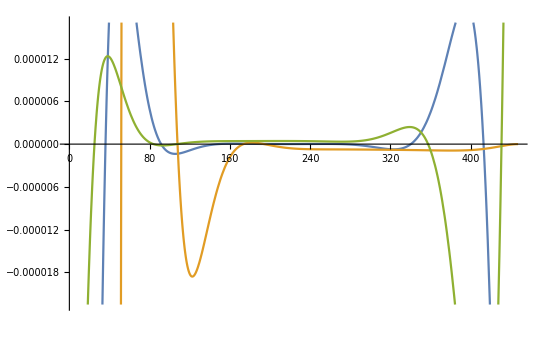

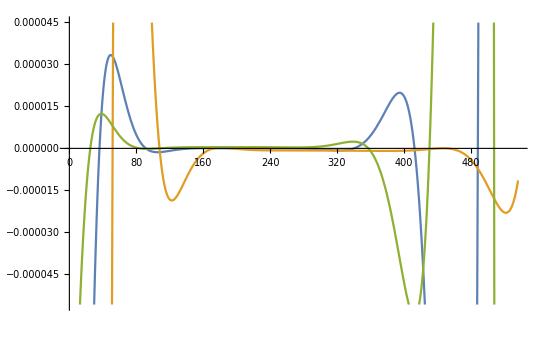

```mathematica
(*Суммарные значения функций - перемножаем найденные гармоники на соответсвующие синусы или косинусы*)
uSeries=(uk[S]/.#&/@resultsAll) [[All,1]];(*Воисхитительный костыль! Как же я люблю местный синтаксис*)
uSum[S_,ϕ_]=cosines[ϕ].uSeries;
wSeries=(wk[S]/.#&/@resultsAll) [[All,1]];
wSum[S_,ϕ_]=cosines[ϕ].wSeries;
vSeries=(vk[S]/.#&/@resultsAll) [[All,1]];
vSum[S_,ϕ_]=sines[ϕ].vSeries;

Plot[{uSum[S,0],vSum[S,Pi/2],wSum[S,0]},{S,0,Smax}]
Plot[{uSum[S,0],vSum[S,Pi/2],wSum[S,0]},{S,0,1.2*Smax}]
(*Plot[uSum[S,0]/.resultsk,{S,0,Smax/.Data}]
Plot[vSum[S,Pi/2]/.resultsk,{S,0,Smax/.Data}]
Plot[wSum[S,0]/.resultsk,{S,0,Smax/.Data}]*)
```

```mathematica
(*Матрица поворота для преобразования координат*)
(*Сначала поворот вокруг оси X на угол Pi-θ, потом поворот вокруг Z на угол ϕ*)
Tmatr1[ϕ_]={{1,0,0},{0,Cos[Pi-θ],-Sin[Pi-θ]},{0,Sin[Pi-θ],Cos[Pi-θ]}}/.rData/.Data;
Tmatr2[ϕ_]={{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}/.rData/.Data;
Tmatr[ϕ_]=Tmatr2[ϕ].Tmatr1[ϕ];
Tmatr[ϕ]//MatrixForm
(*Имеем матрицу перехода из базиса XYZ в базис T1T2N. Для рисования перемещений нужна обратная*)
TmatrInv[ϕ_]=Simplify[Inverse[Tmatr[ϕ]],Assumptions->{Element[ϕ,Reals]}];
(*А вообще, матрица поворота ортогональная, так що просто возьмем транспонированную*)

TmatrInv[ϕ_]=Transpose[Tmatr[ϕ]];
TmatrInv[ϕ]//MatrixForm
```

(Cos[ϕ] | 0.+0.447214 Sin[ϕ] | 0.+0.894427 Sin[ϕ]
Sin[ϕ] | 0.-0.447214 Cos[ϕ] | 0.-0.894427 Cos[ϕ]
0 | 0.894427 | -0.447214)

(Cos[ϕ] | Sin[ϕ] | 0
0.+0.447214 Sin[ϕ] | 0.-0.447214 Cos[ϕ] | 0.894427
0.+0.894427 Sin[ϕ] | 0.-0.894427 Cos[ϕ] | -0.447214)

```mathematica
(*Просто штука, которая рисует исходный и подвижный базисы на конусе. Круто же!*)

arrowCoeff=0.2;
basBeg[S0_,ϕ0_]={Xcone,Ycone,Zcone}/.{S->S0,ϕ->ϕ0};

xArrow[S_,ϕ_]:=Graphics3D[{Red,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*{1,0,0}}]}];
yArrow[S_,ϕ_]:=Graphics3D[{Green,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*{0,1,0}}]}];
zArrow[S_,ϕ_]:=Graphics3D[{Blue,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*{0,0,1}}]}];
drawBasisXYZ[S_,ϕ_]:={xArrow[S,ϕ],yArrow[S,ϕ],zArrow[S,ϕ]};



nArrow2[S_,ϕ_]:=Graphics3D[{Red,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*Tmatr[ϕ].{1,0,0}}]}]; (*Бывший вектор X*)
t2Arrow2[S_,ϕ_]:=Graphics3D[{Green,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*Tmatr[ϕ].{0,1,0}}]}]; (*Бывший вектор Y*)t1Arrow2[S_,ϕ_]:=Graphics3D[{Blue,Arrow[{basBeg[S,ϕ],basBeg[S,ϕ]+arrowCoeff*Tmatr[ϕ].{0,0,1}}]}]; (*Бывший вектор Z*)
drawBasisT1T2N[S_,ϕ_]:={t1Arrow2[S,ϕ],t2Arrow2[S,ϕ],nArrow2[S,ϕ]};
Show[{conePlot ,drawBasisXYZ[0,0],drawBasisT1T2N[Smax/2/.Data,Pi/3],waterPlot},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*Нарисуем деформированную оболочку*)
dispScale=20000;
displVec[S_,ϕ_]={uSum[S,ϕ], vSum[S,ϕ], -wSum[S,ϕ]};
{XconeDef,YconeDef,ZconeDef}={Xcone,Ycone, Zcone}+dispScale*TmatrInv[ϕ].displVec[S,ϕ];
coneDefPlot=ParametricPlot3D[{XconeDef,YconeDef,ZconeDef},{ϕ,-Pi,Pi},{S,0,Smax/.Data},AxesLabel->{"x","y","z"}];
Show[coneDefPlot,waterPlot]
```

-Graphics3D-